```mathematica
q=0.3; α=0.2;
```

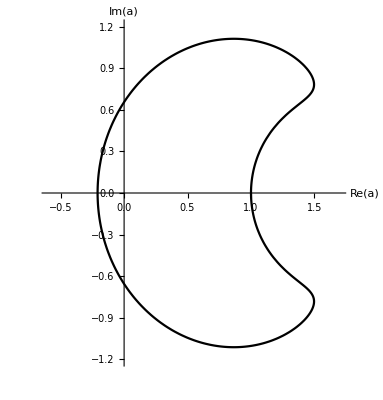

```mathematica
f1=ParametricPlot[ReIm[1+Exp[I*theta] QPochhammer[Exp[-I*theta],q]/QPochhammer[q^α Exp[-I*theta],q]],{theta,0,2Pi},PlotStyle->Black,AxesLabel->{"Re(a)","Im(a)"},PlotRange->{{-0.6,1.7},{-1.2,1.2}}]
```

```mathematica
b=Import["C:\\Users\\Sachin\\AppData\\Local\\Programs\\Microsoft VS Code\\blue.csv"];
g=Import["C:\\Users\\Sachin\\AppData\\Local\\Programs\\Microsoft VS Code\\green.csv"];
o=Import["C:\\Users\\Sachin\\AppData\\Local\\Programs\\Microsoft VS Code\\orange.csv"];
```

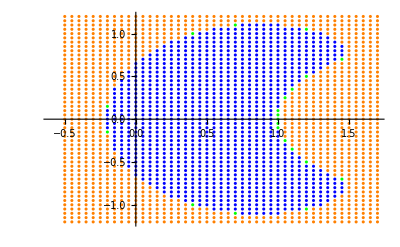

```mathematica
f2=ListPlot[{b,g,o},PlotStyle->{Blue,Green,Orange},PlotRange->{{-0.6,1.7},{-1.2,1.2}}]
```

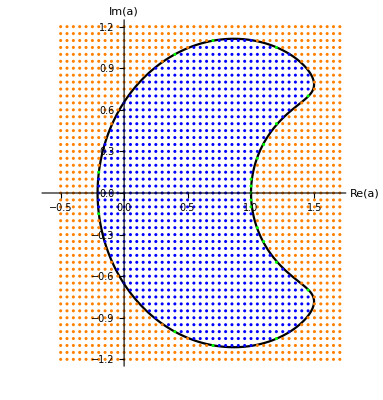

```mathematica
Show[f1,f2]
```

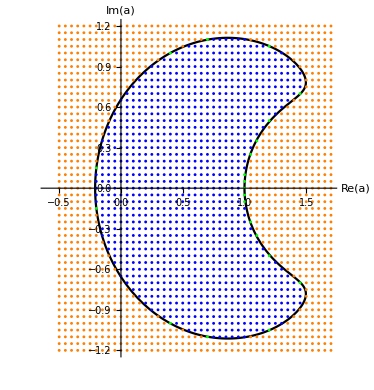
```mathematica
Export["fig8a.pdf",-Graphics-]
```

fig8a.pdf

```mathematica
------------------
```

```mathematica
q=0.2; α=0.5;
```

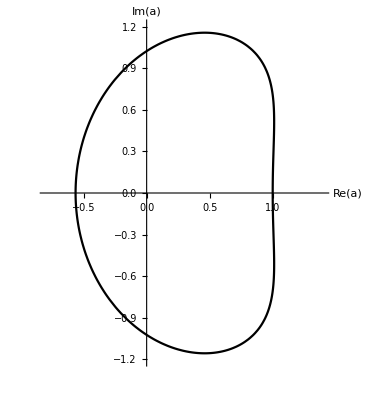

```mathematica
f1=ParametricPlot[ReIm[1+Exp[I*theta] QPochhammer[Exp[-I*theta],q]/QPochhammer[q^α Exp[-I*theta],q]],{theta,0,2Pi},PlotStyle->Black,AxesLabel->{"Re(a)","Im(a)"},PlotRange->{{-0.8,1.4},{-1.2,1.2}}]
```

```mathematica
0.8+1.4
```

2.2

```mathematica
2.2/0.05
```

44.